# The Fibonacci Chain

First load the TriCats package and load the standard library to access oft-used diagrams:

```mathematica
SetDirectory[NotebookDirectory[]];
If[FileExistsQ@#,SetDirectory[(Get@#)@$UserName]]&@"packagelocation";
<<TriCats`;
LoadLibrary["stdlib"];
```

Load diagrams:
- C4Atoms denotes the list of zero- and one-faced diagrams in C_4;
- cap and cup denote the obvious diagrams;
- line denotes a straight line diagram;
- trivalentb (short for “trivalent branch”) denotes the trivalent vertex with one ingoing and two outgoing legs.

```mathematica
Move2Down=DiagramMoveDown[#,2]&;
C4Atoms=Move2Down/@Retrieve["stdlib:C4Atoms"];
cap=Retrieve["stdlib:Cap"];
cup=Retrieve["stdlib:Cup"];
line=Retrieve["stdlib:Line"];
trivalentb=Retrieve["stdlib:TrivalentBranch"];
```

```mathematica
so3qbasisrule=x_Diagram/;IsomorphicDiagramQ[x,C4Atoms⟦4⟧]->{-1/(d-1),1/(d-1),1}.C4Atoms⟦1;;3⟧;
fibdt={d->1/2(1+√5),t->1/2 (1-√5),b->1};
fibbasisrule=x_Diagram/;IsomorphicDiagramQ[x,C4Atoms⟦3⟧]->{1,-1/d}.C4Atoms⟦1;;2⟧;
fibbeta=FullSimplify[Exp[ⅈ(n-1)/n π]/.n->5];
fibbraiding={1,fibbeta}.C4Atoms⟦1;;2⟧;
```

```mathematica
YangBaxter[braiding_,line_]:={DiagramCompose[DiagramTensor[braiding,line],DiagramTensor[line,braiding],DiagramTensor[braiding,line]],DiagramCompose[DiagramTensor[line,braiding],DiagramTensor[braiding,line],DiagramTensor[line,braiding]]}
```

```mathematica
VTensor[braiding_,trivalentb_,line_,cup_,cap_]:=DiagramCompose[DiagramTensor[line,trivalentb,cup],DiagramTensor[braiding,DiagramConjugate[braiding],line],DiagramTensor[line,trivalentb,line,line,line],DiagramTensor[line,line,cap,line,line]];
```

```mathematica
AscendingOp[v_,line_]:=Function[x,DiagramCompose[v,DiagramTensor[x,line,line],DiagramConjugate[v]]];
```

```mathematica
FusionOp[v_,line_]:=Function[{x,y},DiagramCompose[v,DiagramTensor[x,y],DiagramConjugate[v]]]
```

## Braiding test

First we check that fibbraiding is indeed a braiding.
Biunitarity:

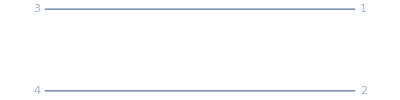
Diagram[-Graphics-,{1,2},{3,4}]

```mathematica
FullSimplify[ReduceDiagram[DiagramCompose[DiagramConjugate[fibbraiding],fibbraiding],dimC4->2]/.fibdt]//EnsureGraph
```

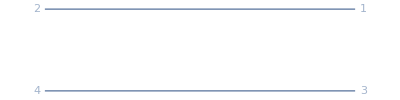
Diagram[-Graphics-,{1,2},{3,4}]

```mathematica
FullSimplify[ReduceDiagram[DiagramCompose[DiagramTensor[line,cup,line],DiagramTensor[DiagramConjugate[fibbraiding],fibbraiding],DiagramTensor[line,cap,line]],dimC4->2]/.fibdt]//EnsureGraph
```

```mathematica
fibcheckYB=ReduceDiagram[Subtract@@YangBaxter[fibbraiding,line],dimC4->2];
```

```mathematica
FullSimplify[Components[fibcheckYB,DistinctDiagrams[fibcheckYB]]/.fibdt]
```

{0,0,0,0,0}

## The chain example

```mathematica
fibv=ReduceDiagram[VTensor[fibbraiding,trivalentb,line,cup,cap],dimC4->2];
```

```mathematica
fibascending=AscendingOp[fibv,line];
```

```mathematica
fibvmatrix=RootReduce@Transpose[
FullSimplify[
Components[ReduceDiagram[fibascending[#],b->1,dimC4->2]//.{so3qbasisrule,fibbasisrule}//.fibdt,C4Atoms⟦1;;2⟧]
]&/@C4Atoms⟦1;;2⟧
]
```

{{1,1/2 (3-√5)},{0,1/2 (3-√5)}}

```mathematica
{fibveigenvalues,fibveigenvectors}=Eigensystem[fibvmatrix]//RootReduce
```

{{1,1/2 (3-√5)},{{1,0},{1/2 (1-√5),1}}}

```mathematica
-Log2[#]&/@fibveigenvalues//N
```

{0.,1.38848}

```mathematica
fibfusion=FusionOp[fibv,line];
```

```mathematica
fibfusionmatrix=FullSimplify[
Table[Components[ReduceDiagram[fibfusion[fibveigenvectors⟦i⟧.C4Atoms⟦1;;2⟧,fibveigenvectors⟦j⟧.C4Atoms⟦1;;2⟧],b->1,dimC4->3]//.{so3qbasisrule,fibbasisrule}//.fibdt,C4Atoms⟦1;;2⟧],
{i,1,2},{j,1,2}]]
```

{{{1,0},{2-√5,1/2 (3-√5)}},{{2-√5,1/2 (3-√5)},{1/2 (11-5 √5),5-2 √5}}}

The fusion coefficients f_γ^αβ:

```mathematica
fibfusioncoefficients=Table[FullSimplify[LinearSolve[Transpose@fibveigenvectors,fibfusionmatrix⟦i,j⟧]],{i,1,2},{j,1,2}]
```

{{{1,0},{0,1/2 (3-√5)}},{{0,1/2 (3-√5)},{-2+√5,5-2 √5}}}

The fusion matrix N_γ^αβ:

```mathematica
fibN=Map[Boole@FullSimplify[#≠0]&,fibfusioncoefficients,{3}]
```

{{{1,0},{0,1}},{{0,1},{1,1}}}

```mathematica
fibN⟦1,;;⟧//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
fibN⟦2,;;⟧//MatrixForm
```

(0 | 1
1 | 1)